```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["all-topics-keywords.txt"];
```

```mathematica
lines=StringTrim/@StringSplit[ToLowerCase[data],"\n"];
names=Select[lines,StringEndsQ[#,":"]&];
words=Select[lines,!StringEndsQ[#,":"]&&!#==""&];
```

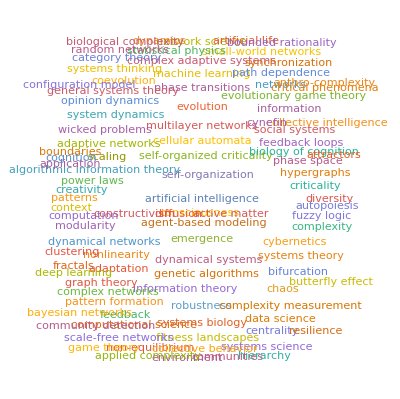

```mathematica
WordCloud[words,FontFamily->"Helvetica",WordSpacings->3]
```

```mathematica
unique=Union[words];
```

```mathematica
(*Do[
If[EditDistance[unique[[i]],unique[[j]]]<3,Print[unique[[i]]," ",unique[[j]]]]
,{i,Length[unique]-1}
,{j,i+1,Length[unique]}]*)
```

```mathematica
freqs=SortBy[Tally[words],-Last[#]&];
```

```mathematica
topranked=Reverse[Select[freqs,#[[2]]>=3&]];
```

```mathematica
numTopranked=topranked//Length
```

73

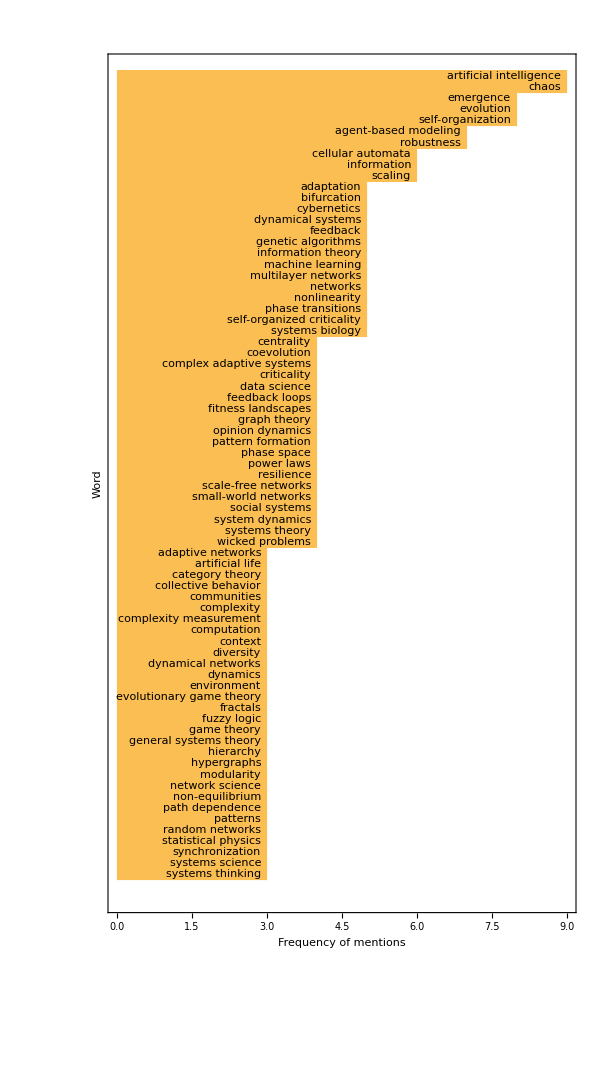

```mathematica
BarChart[Last/@topranked,BarOrigin->Left,ChartLabels->Placed[First/@topranked,Right],Frame->True,AspectRatio->1.8,LabelStyle->Directive[Medium,Black],FrameLabel->{"Word","Frequency of mentions"},ImageSize->600]
```

```mathematica
OAcountBaseline[w_]:=Module[{wr,url,result},
wr=StringReplace[w,{" "->"%20"}];
url="https://api.openalex.org/works?filter=default.search%3A%22"<>wr<>"%22";
result=Import[url];
<|<|result|>["meta"]|>["count"]
];
```

```mathematica
Monitor[
OAcountresultsBaseline=Table[Pause[0.1];v=OAcountBaseline[w];{w,v},{w,unique}];
,{w,v}
]
```

```mathematica
Export["OAcountresultsBaseline.csv",OAcountresultsBaseline];
```

OAcountresultsBaseline.csv

```mathematica
OAcount[w_]:=Module[{wr,url,result},
wr=StringReplace[w,{" "->"%20"}];
url="https://api.openalex.org/works?filter=default.search%3A%22complex%20system%22%20OR%20%22complexity%20science%22,default.search%3A%22"<>wr<>"%22";
result=Import[url];
<|<|result|>["meta"]|>["count"]
];
```

```mathematica
Monitor[
OAcountresults=Table[Pause[0.1];v=OAcount[w];{w,v},{w,unique}];
,{w,v}
]
```

```mathematica
Export["OAcountresults.csv",OAcountresults];
```

```mathematica
OAcountresultsBaseline=Import["OAcountresultsBaseline.csv"];
OAcountresults=Import["OAcountresults.csv"];
```

```mathematica
Do[
If[!NumberQ[OAcountresultsBaseline[[i,2]]],OAcountresultsBaseline[[i,2]]=0]
,{i,Length[OAcountresultsBaseline]}
]
Do[
If[!NumberQ[OAcountresults[[i,2]]],OAcountresults[[i,2]]=0]
,{i,Length[OAcountresults]}
]
```

```mathematica
OAcountresultsBaselineAssoc=<|Rule@@#&/@OAcountresultsBaseline|>;
OAcountresultsAssoc=<|Rule@@#&/@OAcountresults|>;
```

```mathematica
words=First/@OAcountresults;
resultsBaselineSum=Total[Last/@OAcountresultsBaseline];
resultsSum=Total[Last/@OAcountresults];
```

```mathematica
VB=Table[
{w,If[OAcountresultsBaselineAssoc[w]==0,0,N[(OAcountresultsAssoc[w]/resultsSum)/(OAcountresultsBaselineAssoc[w]/resultsBaselineSum)]]}
,{w,words}
];
```

```mathematica
meanAssoc=Mean[OAcountresultsAssoc//Values]//N;
```

```mathematica
relevance=Table[{x[[1]],x[[2]]OAcountresultsAssoc[x[[1]]]/meanAssoc},{x,VB}]/.Indeterminate->0;
```

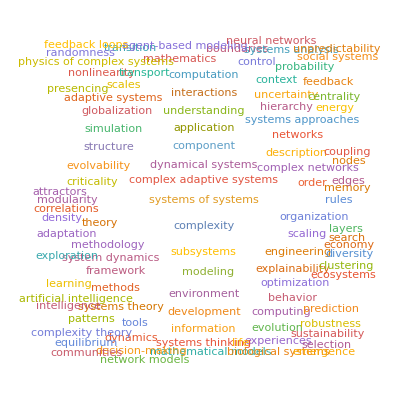

```mathematica
WordCloud[#[[2]]->#[[1]]&/@relevance,FontFamily->"Helvetica",WordSpacings->3]
```

```mathematica
topranked2=SortBy[relevance,Last][[-numTopranked;;]];
```

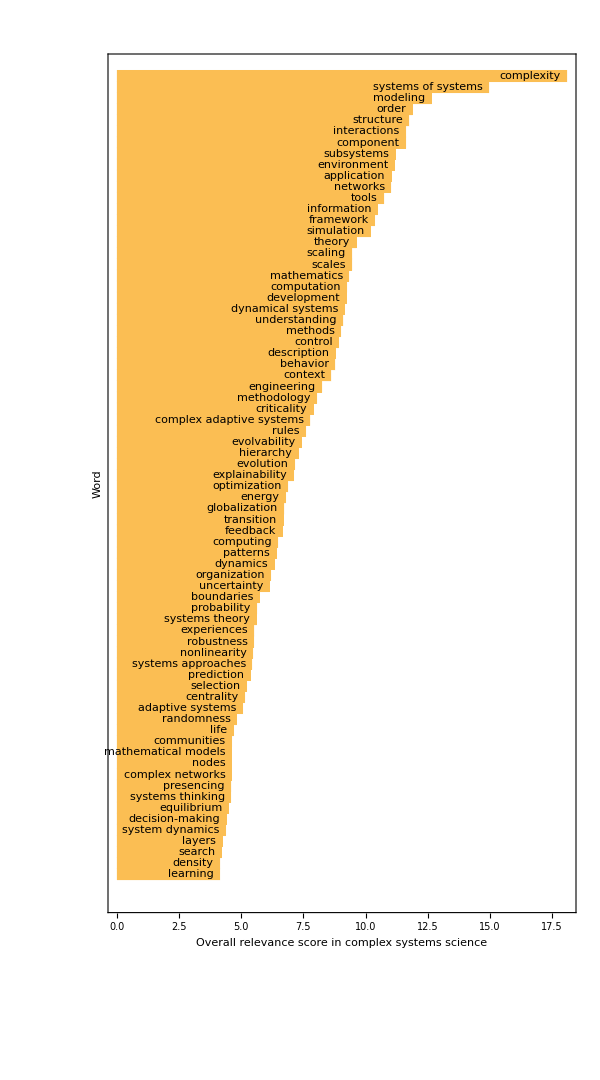

```mathematica
BarChart[Last/@topranked2,BarOrigin->Left,ChartLabels->Placed[First/@topranked2,Right],Frame->True,AspectRatio->1.8,LabelStyle->Directive[Medium,Black],FrameLabel->{"Word","Overall relevance score in complex systems science"},ImageSize->600]
```

```mathematica
Export["relevance-scores.csv",relevance];
```

relevance-scores.csv

```mathematica
OAlink[w1_,w2_]:=Module[{w1r,w2r,url,result},
w1r=StringReplace[w1,{" "->"%20"}];
w2r=StringReplace[w2,{" "->"%20"}];
url="https://api.openalex.org/works?filter=default.search%3A%22complex%20system%22%20OR%20%22complexity%20science%22,default.search%3A%22"<>w1r<>"%22,default.search%3A%22"<>w2r<>"%22";
result=Import[url];
<|<|result|>["meta"]|>["count"]
];
```

```mathematica
numKeywords=300;
relevance=<|Rule@@#&/@(SortBy[Import["relevance-scores.csv"],Last][[-numKeywords;;]])|>;
mostRelevant=Keys[relevance];
```

```mathematica
additionalWords=Complement[First/@topranked,mostRelevant]
```

{adaptive networks,category theory,complexity measurement,data science,evolutionary game theory,fitness landscapes,hypergraphs,multilayer networks,opinion dynamics,path dependence}

```mathematica
searched=Sort[Join[mostRelevant,additionalWords]];
```

```mathematica
f=OpenWrite["OAlinkresults-all-at-once.csv"];
Monitor[
Do[
Pause[0.1];
w1=searched[[i]];
w2=searched[[j]];
v=OAlink[w1,w2];
Write[f,{w1,w2,v}];
,{i,Length[searched]-1}
,{j,i+1,Length[searched]}
];
,{w1,w2,v}
]
Close[f];
```